```mathematica
<<X`
```

Package-X v2.1.1 already initialized
For more information, see the

```mathematica
Clear[g]
```

```mathematica
Γ[i_][j_]:=g[i][j]Exp[I*ϕ[i][j]](Cos[θ[i][j]]𝟙+I*Exp[I*δ[i][j]]Sin[θ[i][j]]γ5);
Γb[i_][j_]:=g[i][j]Exp[-I*ϕ[i][j]](Cos[θ[i][j]]𝟙+I*Exp[-I*δ[i][j]]Sin[θ[i][j]]γ5);
```

```mathematica
choice1={ϕkl->ϕik};
choice2=;
```

```mathematica
p(SuperMinus[i])==p1(SuperMinus[j])+p2(SuperMinus[k])+p3(SuperPlus[l])
```

```mathematica
(p-p1)^2==p^2+p1^2-2p.p1==(p2+p3)^2==s23->p.p1==-1/2(s23-mi^2-mj^2)
```

```mathematica
(p-p2)^2==p^2+p2^2-2p.p2==(p1+p3)^2==s13->p.p2==-1/2(s13-mi^2-mk^2)
```

```mathematica
p1.p3==1/2(s13-mj^2-ml^2);
p2.p3==1/2(s23-mk^2-ml^2);
```

```mathematica
p.p3==(p1+p2+p3).p3==p1.p3+p2.p3+p3.p3==1/2(s13-mj^2-ml^2)+1/2(s23-mk^2-ml^2)+ml^2==1/2(s13+s23)-1/2(mj^2+mk^2)
```

```mathematica
p1.p2==(p-p2-p3).p2==p.p2-p2.p2-p2.p3==-1/2(s13-mi^2-mk^2)-mk^2-1/2(s23-mk^2-ml^2)==-1/2(s13+s23)+1/2(mi^2+ml^2)
```

```mathematica
p1.p2==1/2(s12-mj^2-mk^2)
```

```mathematica
kinematics={p.p->mi^2,p1.p1->mj^2,p2.p2->mk^2,p3.p3->ml^2,p.p1->-1/2(s23-mi^2-mj^2),p.p2->-1/2(s13-mi^2-mk^2),p.p3->1/2(s13+s23)-1/2(mj^2+mk^2),p1.p2->-1/2(s13+s23)+1/2(mi^2+ml^2),p1.p3->1/2(s13-mj^2-ml^2),p2.p3->1/2(s23-mk^2-ml^2),p->p1+p2+p3};
```

```mathematica
M2323=FullSimplify[(1/2 1/((s23-M^2)^2)Spur[(γ.p1-mj*𝟙),VertexJI,(γ.p-mi*𝟙),VertexIJ]Spur[(γ.p2-mk*𝟙),VertexKL,(γ.p3+ml*𝟙),VertexLK])/.kinematics];
M1313=FullSimplify[(1/2 1/((s13-M^2)^2)Spur[(γ.p2-mk*𝟙),VertexKI,(γ.p-mi*𝟙),VertexIK]Spur[(γ.p1-mj*𝟙),VertexJL,(γ.p3+ml*𝟙),VertexLJ])/.kinematics];
```

```mathematica
M2323
```

-(2 gij^2 gkl^2 (mi^2+mj^2-s23+2 mi mj Cos[2 θij]) (mk^2+ml^2-s23+2 mk ml Cos[2 θkl]))/((M^2-s23)^2)

```mathematica
M1313
```

-(2 gik^2 gjl^2 (mi^2+mk^2-s13+2 mi mk Cos[2 θik]) (mj^2+ml^2-s13+2 mj ml Cos[2 θjl]))/((M^2-s13)^2)

```mathematica
M1323=(1/2 1/((s13-M^2)(s23-M^2))(Spur[(γ.p1-mj*𝟙),VertexJI,(γ.p-mi*𝟙),VertexIK,(γ.p2-mk*𝟙),VertexKL,(γ.p3+ml*𝟙),VertexLJ]+Spur[VertexJL,(γ.p3+ml*𝟙),VertexLK,(γ.p2-mk*𝟙),VertexKI,(γ.p-mi*𝟙),VertexIJ,(γ.p1-mj*𝟙)]))/.kinematics;
```

```mathematica
FullSimplify[Expand[((-M^2+s13) (-M^2+s23))/(gij*gik*gjl*gkl)M1323/.{mj->0,mk->0,ml->0,Subscript[ε, {p1},{p2},{p3},{p1+p2+p3}]->0}]]
```

$Aborted

```mathematica
Subscript[ε, {p},{p1},{p2},{p3}]
```

1/(2 gij gik gjl gkl)(-4 ⅇ^(ⅈ ϕij-ⅈ ϕik+ⅈ ϕjl-ⅈ ϕkl) gij gik gjl gkl mi mj mk ml Cos[θij] Cos[θik] Cos[θjl] Cos[θkl]-4 ⅇ^(-ⅈ ϕij+ⅈ ϕik-ⅈ ϕjl+ⅈ ϕkl) gij gik gjl gkl mi mj mk ml Cos[θij] Cos[θik] Cos[θjl] Cos[θkl]-2 ⅇ^(ⅈ ϕij-ⅈ ϕik+ⅈ ϕjl-ⅈ ϕkl) gij gik gjl gkl mj ml (mi^2+mk^2-s13) Cos[θij] Cos[θik] Cos[θjl] Cos[θkl]-2 ⅇ^(-ⅈ ϕij+ⅈ ϕik-ⅈ ϕjl+ⅈ ϕkl) gij gik gjl gkl mj ml (mi^2+mk^2-s13) Cos[θij] Cos[θik] Cos[θjl] Cos[θkl]+2 ⅇ^(ⅈ ϕij-ⅈ ϕik+ⅈ ϕjl-ⅈ ϕkl) gij gik gjl gkl mi mk (-mj^2-ml^2+s13) Cos[θij] Cos[θik] Cos[θjl] Cos[θkl]+2 ⅇ^(-ⅈ ϕij+ⅈ ϕik-ⅈ ϕjl+ⅈ ϕkl) gij gik gjl gkl mi mk (-mj^2-ml^2+s13) Cos[θij] Cos[θik] Cos[θjl] Cos[θkl]+ⅇ^(ⅈ ϕij-ⅈ ϕik+ⅈ ϕjl-ⅈ ϕkl) gij gik gjl gkl (mi^2+mk^2-s13) (-mj^2-ml^2+s13) Cos[θij] Cos[θik] Cos[θjl] Cos[θkl]+ⅇ^(-ⅈ ϕij+ⅈ ϕik-ⅈ ϕjl+ⅈ ϕkl) gij gik gjl gkl (mi^2+mk^2-s13) (-mj^2-ml^2+s13) Cos[θij] Cos[θik] Cos[θjl] Cos[θkl]-4 ⅇ^(ⅈ ϕij-ⅈ ϕik+ⅈ ϕjl-ⅈ ϕkl) gij gik gjl gkl mi ml (1/2 (mi^2+ml^2)+1/2 (-s13-s23)) Cos[θij] Cos[θik] Cos[θjl] Cos[θkl]-4 ⅇ^(-ⅈ ϕij+ⅈ ϕik-ⅈ ϕjl+ⅈ ϕkl) gij gik gjl gkl mi ml (1/2 (mi^2+ml^2)+1/2 (-s13-s23)) Cos[θij] Cos[θik] Cos[θjl] Cos[θkl]-2 ⅇ^(ⅈ ϕij-ⅈ ϕik+ⅈ ϕjl-ⅈ ϕkl) gij gik gjl gkl mk ml (mi^2+mj^2-s23) Cos[θij] Cos[θik] Cos[θjl] Cos[θkl]-2 ⅇ^(-ⅈ ϕij+ⅈ ϕik-ⅈ ϕjl+ⅈ ϕkl) gij gik gjl gkl mk ml (mi^2+mj^2-s23) Cos[θij] Cos[θik] Cos[θjl] Cos[θkl]+2 ⅇ^(ⅈ ϕij-ⅈ ϕik+ⅈ ϕjl-ⅈ ϕkl) gij gik gjl gkl mi mj (-mk^2-ml^2+s23) Cos[θij] Cos[θik] Cos[θjl] Cos[θkl]+2 ⅇ^(-ⅈ ϕij+ⅈ ϕik-ⅈ ϕjl+ⅈ ϕkl) gij gik gjl gkl mi mj (-mk^2-ml^2+s23) Cos[θij] Cos[θik] Cos[θjl] Cos[θkl]+ⅇ^(ⅈ ϕij-ⅈ ϕik+ⅈ ϕjl-ⅈ ϕkl) gij gik gjl gkl (mi^2+mj^2-s23) (-mk^2-ml^2+s23) Cos[θij] Cos[θik] Cos[θjl] Cos[θkl]+ⅇ^(-ⅈ ϕij+ⅈ ϕik-ⅈ ϕjl+ⅈ ϕkl) gij gik gjl gkl (mi^2+mj^2-s23) (-mk^2-ml^2+s23) Cos[θij] Cos[θik] Cos[θjl] Cos[θkl]+4 ⅇ^(ⅈ ϕij-ⅈ ϕik+ⅈ ϕjl-ⅈ ϕkl) gij gik gjl gkl mj mk (1/2 (-mj^2-mk^2)+(s13+s23)/2) Cos[θij] Cos[θik] Cos[θjl] Cos[θkl]+4 ⅇ^(-ⅈ ϕij+ⅈ ϕik-ⅈ ϕjl+ⅈ ϕkl) gij gik gjl gkl mj mk (1/2 (-mj^2-mk^2)+(s13+s23)/2) Cos[θij] Cos[θik] Cos[θjl] Cos[θkl]-4 ⅇ^(ⅈ ϕij-ⅈ ϕik+ⅈ ϕjl-ⅈ ϕkl) gij gik gjl gkl (1/2 (mi^2+ml^2)+1/2 (-s13-s23)) (1/2 (-mj^2-mk^2)+(s13+s23)/2) Cos[θij] Cos[θik] Cos[θjl] Cos[θkl]-4 ⅇ^(-ⅈ ϕij+ⅈ ϕik-ⅈ ϕjl+ⅈ ϕkl) gij gik gjl gkl (1/2 (mi^2+ml^2)+1/2 (-s13-s23)) (1/2 (-mj^2-mk^2)+(s13+s23)/2) Cos[θij] Cos[θik] Cos[θjl] Cos[θkl]+4 ⅇ^(ⅈ δij+ⅈ ϕij-ⅈ ϕik+ⅈ ϕjl-ⅈ ϕkl) gij gik gjl gkl Cos[θik] Cos[θjl] Cos[θkl] ε_({p},{p1},{p2},{p3}) Sin[θij]+4 ⅇ^(-ⅈ δij-ⅈ ϕij+ⅈ ϕik-ⅈ ϕjl+ⅈ ϕkl) gij gik gjl gkl Cos[θik] Cos[θjl] Cos[θkl] ε_({p},{p1},{p2},{p3}) Sin[θij]-4 ⅇ^(-ⅈ δik+ⅈ ϕij-ⅈ ϕik+ⅈ ϕjl-ⅈ ϕkl) gij gik gjl gkl Cos[θij] Cos[θjl] Cos[θkl] ε_({p},{p1},{p2},{p3}) Sin[θik]-4 ⅇ^(ⅈ δik-ⅈ ϕij+ⅈ ϕik-ⅈ ϕjl+ⅈ ϕkl) gij gik gjl gkl Cos[θij] Cos[θjl] Cos[θkl] ε_({p},{p1},{p2},{p3}) Sin[θik]+4 ⅇ^(ⅈ δij-ⅈ δik+ⅈ ϕij-ⅈ ϕik+ⅈ ϕjl-ⅈ ϕkl) gij gik gjl gkl mi mj mk ml Cos[θjl] Cos[θkl] Sin[θij] Sin[θik]+4 ⅇ^(-ⅈ δij+ⅈ δik-ⅈ ϕij+ⅈ ϕik-ⅈ ϕjl+ⅈ ϕkl) gij gik gjl gkl mi mj mk ml Cos[θjl] Cos[θkl] Sin[θij] Sin[θik]-2 ⅇ^(ⅈ δij-ⅈ δik+ⅈ ϕij-ⅈ ϕik+ⅈ ϕjl-ⅈ ϕkl) gij gik gjl gkl mj ml (mi^2+mk^2-s13) Cos[θjl] Cos[θkl] Sin[θij] Sin[θik]-2 ⅇ^(-ⅈ δij+ⅈ δik-ⅈ ϕij+ⅈ ϕik-ⅈ ϕjl+ⅈ ϕkl) gij gik gjl gkl mj ml (mi^2+mk^2-s13) Cos[θjl] Cos[θkl] Sin[θij] Sin[θik]-2 ⅇ^(ⅈ δij-ⅈ δik+ⅈ ϕij-ⅈ ϕik+ⅈ ϕjl-ⅈ ϕkl) gij gik gjl gkl mi mk (-mj^2-ml^2+s13) Cos[θjl] Cos[θkl] Sin[θij] Sin[θik]-2 ⅇ^(-ⅈ δij+ⅈ δik-ⅈ ϕij+ⅈ ϕik-ⅈ ϕjl+ⅈ ϕkl) gij gik gjl gkl mi mk (-mj^2-ml^2+s13) Cos[θjl] Cos[θkl] Sin[θij] Sin[θik]+ⅇ^(ⅈ δij-ⅈ δik+ⅈ ϕij-ⅈ ϕik+ⅈ ϕjl-ⅈ ϕkl) gij gik gjl gkl (mi^2+mk^2-s13) (-mj^2-ml^2+s13) Cos[θjl] Cos[θkl] Sin[θij] Sin[θik]+ⅇ^(-ⅈ δij+ⅈ δik-ⅈ ϕij+ⅈ ϕik-ⅈ ϕjl+ⅈ ϕkl) gij gik gjl gkl (mi^2+mk^2-s13) (-mj^2-ml^2+s13) Cos[θjl] Cos[θkl] Sin[θij] Sin[θik]+4 ⅇ^(ⅈ δij-ⅈ δik+ⅈ ϕij-ⅈ ϕik+ⅈ ϕjl-ⅈ ϕkl) gij gik gjl gkl mi ml (1/2 (mi^2+ml^2)+1/2 (-s13-s23)) Cos[θjl] Cos[θkl] Sin[θij] Sin[θik]+4 ⅇ^(-ⅈ δij+ⅈ δik-ⅈ ϕij+ⅈ ϕik-ⅈ ϕjl+ⅈ ϕkl) gij gik gjl gkl mi ml (1/2 (mi^2+ml^2)+1/2 (-s13-s23)) Cos[θjl] Cos[θkl] Sin[θij] Sin[θik]-2 ⅇ^(ⅈ δij-ⅈ δik+ⅈ ϕij-ⅈ ϕik+ⅈ ϕjl-ⅈ ϕkl) gij gik gjl gkl mk ml (mi^2+mj^2-s23) Cos[θjl] Cos[θkl] Sin[θij] Sin[θik]-2 ⅇ^(-ⅈ δij+ⅈ δik-ⅈ ϕij+ⅈ ϕik-ⅈ ϕjl+ⅈ ϕkl) gij gik gjl gkl mk ml (mi^2+mj^2-s23) Cos[θjl] Cos[θkl] Sin[θij] Sin[θik]-2 ⅇ^(ⅈ δij-ⅈ δik+ⅈ ϕij-ⅈ ϕik+ⅈ ϕjl-ⅈ ϕkl) gij gik gjl gkl mi mj (-mk^2-ml^2+s23) Cos[θjl] Cos[θkl] Sin[θij] Sin[θik]-2 ⅇ^(-ⅈ δij+ⅈ δik-ⅈ ϕij+ⅈ ϕik-ⅈ ϕjl+ⅈ ϕkl) gij gik gjl gkl mi mj (-mk^2-ml^2+s23) Cos[θjl] Cos[θkl] Sin[θij] Sin[θik]+ⅇ^(ⅈ δij-ⅈ δik+ⅈ ϕij-ⅈ ϕik+ⅈ ϕjl-ⅈ ϕkl) gij gik gjl gkl (mi^2+mj^2-s23) (-mk^2-ml^2+s23) Cos[θjl] Cos[θkl] Sin[θij] Sin[θik]+ⅇ^(-ⅈ δij+ⅈ δik-ⅈ ϕij+ⅈ ϕik-ⅈ ϕjl+ⅈ ϕkl) gij gik gjl gkl (mi^2+mj^2-s23) (-mk^2-ml^2+s23) Cos[θjl] Cos[θkl] Sin[θij] Sin[θik]+4 ⅇ^(ⅈ δij-ⅈ δik+ⅈ ϕij-ⅈ ϕik+ⅈ ϕjl-ⅈ ϕkl) gij gik gjl gkl mj mk (1/2 (-mj^2-mk^2)+(s13+s23)/2) Cos[θjl] Cos[θkl] Sin[θij] Sin[θik]+4 ⅇ^(-ⅈ δij+ⅈ δik-ⅈ ϕij+ⅈ ϕik-ⅈ ϕjl+ⅈ ϕkl) gij gik gjl gkl mj mk (1/2 (-mj^2-mk^2)+(s13+s23)/2) Cos[θjl] Cos[θkl] Sin[θij] Sin[θik]-4 ⅇ^(ⅈ δij-ⅈ δik+ⅈ ϕij-ⅈ ϕik+ⅈ ϕjl-ⅈ ϕkl) gij gik gjl gkl (1/2 (mi^2+ml^2)+1/2 (-s13-s23)) (1/2 (-mj^2-mk^2)+(s13+s23)/2) Cos[θjl] Cos[θkl] Sin[θij] Sin[θik]-4 ⅇ^(-ⅈ δij+ⅈ δik-ⅈ ϕij+ⅈ ϕik-ⅈ ϕjl+ⅈ ϕkl) gij gik gjl gkl (1/2 (mi^2+ml^2)+1/2 (-s13-s23)) (1/2 (-mj^2-mk^2)+(s13+s23)/2) Cos[θjl] Cos[θkl] Sin[θij] Sin[θik]-4 ⅇ^(ⅈ δjl+ⅈ ϕij-ⅈ ϕik+ⅈ ϕjl-ⅈ ϕkl) gij gik gjl gkl Cos[θij] Cos[θik] Cos[θkl] ε_({p},{p1},{p2},{p3}) Sin[θjl]-4 ⅇ^(-ⅈ δjl-ⅈ ϕij+ⅈ ϕik-ⅈ ϕjl+ⅈ ϕkl) gij gik gjl gkl Cos[θij] Cos[θik] Cos[θkl] ε_({p},{p1},{p2},{p3}) Sin[θjl]+4 ⅇ^(ⅈ δij+ⅈ δjl+ⅈ ϕij-ⅈ ϕik+ⅈ ϕjl-ⅈ ϕkl) gij gik gjl gkl mi mj mk ml Cos[θik] Cos[θkl] Sin[θij] Sin[θjl]+4 ⅇ^(-ⅈ δij-ⅈ δjl-ⅈ ϕij+ⅈ ϕik-ⅈ ϕjl+ⅈ ϕkl) gij gik gjl gkl mi mj mk ml Cos[θik] Cos[θkl] Sin[θij] Sin[θjl]+2 ⅇ^(ⅈ δij+ⅈ δjl+ⅈ ϕij-ⅈ ϕik+ⅈ ϕjl-ⅈ ϕkl) gij gik gjl gkl mj ml (mi^2+mk^2-s13) Cos[θik] Cos[θkl] Sin[θij] Sin[θjl]+2 ⅇ^(-ⅈ δij-ⅈ δjl-ⅈ ϕij+ⅈ ϕik-ⅈ ϕjl+ⅈ ϕkl) gij gik gjl gkl mj ml (mi^2+mk^2-s13) Cos[θik] Cos[θkl] Sin[θij] Sin[θjl]+2 ⅇ^(ⅈ δij+ⅈ δjl+ⅈ ϕij-ⅈ ϕik+ⅈ ϕjl-ⅈ ϕkl) gij gik gjl gkl mi mk (-mj^2-ml^2+s13) Cos[θik] Cos[θkl] Sin[θij] Sin[θjl]+2 ⅇ^(-ⅈ δij-ⅈ δjl-ⅈ ϕij+ⅈ ϕik-ⅈ ϕjl+ⅈ ϕkl) gij gik gjl gkl mi mk (-mj^2-ml^2+s13) Cos[θik] Cos[θkl] Sin[θij] Sin[θjl]+ⅇ^(ⅈ δij+ⅈ δjl+ⅈ ϕij-ⅈ ϕik+ⅈ ϕjl-ⅈ ϕkl) gij gik gjl gkl (mi^2+mk^2-s13) (-mj^2-ml^2+s13) Cos[θik] Cos[θkl] Sin[θij] Sin[θjl]+ⅇ^(-ⅈ δij-ⅈ δjl-ⅈ ϕij+ⅈ ϕik-ⅈ ϕjl+ⅈ ϕkl) gij gik gjl gkl (mi^2+mk^2-s13) (-mj^2-ml^2+s13) Cos[θik] Cos[θkl] Sin[θij] Sin[θjl]-4 ⅇ^(ⅈ δij+ⅈ δjl+ⅈ ϕij-ⅈ ϕik+ⅈ ϕjl-ⅈ ϕkl) gij gik gjl gkl mi ml (1/2 (mi^2+ml^2)+1/2 (-s13-s23)) Cos[θik] Cos[θkl] Sin[θij] Sin[θjl]-4 ⅇ^(-ⅈ δij-ⅈ δjl-ⅈ ϕij+ⅈ ϕik-ⅈ ϕjl+ⅈ ϕkl) gij gik gjl gkl mi ml (1/2 (mi^2+ml^2)+1/2 (-s13-s23)) Cos[θik] Cos[θkl] Sin[θij] Sin[θjl]-2 ⅇ^(ⅈ δij+ⅈ δjl+ⅈ ϕij-ⅈ ϕik+ⅈ ϕjl-ⅈ ϕkl) gij gik gjl gkl mk ml (mi^2+mj^2-s23) Cos[θik] Cos[θkl] Sin[θij] Sin[θjl]-2 ⅇ^(-ⅈ δij-ⅈ δjl-ⅈ ϕij+ⅈ ϕik-ⅈ ϕjl+ⅈ ϕkl) gij gik gjl gkl mk ml (mi^2+mj^2-s23) Cos[θik] Cos[θkl] Sin[θij] Sin[θjl]-2 ⅇ^(ⅈ δij+ⅈ δjl+ⅈ ϕij-ⅈ ϕik+ⅈ ϕjl-ⅈ ϕkl) gij gik gjl gkl mi mj (-mk^2-ml^2+s23) Cos[θik] Cos[θkl] Sin[θij] Sin[θjl]-2 ⅇ^(-ⅈ δij-ⅈ δjl-ⅈ ϕij+ⅈ ϕik-ⅈ ϕjl+ⅈ ϕkl) gij gik gjl gkl mi mj (-mk^2-ml^2+s23) Cos[θik] Cos[θkl] Sin[θij] Sin[θjl]+ⅇ^(ⅈ δij+ⅈ δjl+ⅈ ϕij-ⅈ ϕik+ⅈ ϕjl-ⅈ ϕkl) gij gik gjl gkl (mi^2+mj^2-s23) (-mk^2-ml^2+s23) Cos[θik] Cos[θkl] Sin[θij] Sin[θjl]+ⅇ^(-ⅈ δij-ⅈ δjl-ⅈ ϕij+ⅈ ϕik-ⅈ ϕjl+ⅈ ϕkl) gij gik gjl gkl (mi^2+mj^2-s23) (-mk^2-ml^2+s23) Cos[θik] Cos[θkl] Sin[θij] Sin[θjl]-4 ⅇ^(ⅈ δij+ⅈ δjl+ⅈ ϕij-ⅈ ϕik+ⅈ ϕjl-ⅈ ϕkl) gij gik gjl gkl mj mk (1/2 (-mj^2-mk^2)+(s13+s23)/2) Cos[θik] Cos[θkl] Sin[θij] Sin[θjl]-4 ⅇ^(-ⅈ δij-ⅈ δjl-ⅈ ϕij+ⅈ ϕik-ⅈ ϕjl+ⅈ ϕkl) gij gik gjl gkl mj mk (1/2 (-mj^2-mk^2)+(s13+s23)/2) Cos[θik] Cos[θkl] Sin[θij] Sin[θjl]-4 ⅇ^(ⅈ δij+ⅈ δjl+ⅈ ϕij-ⅈ ϕik+ⅈ ϕjl-ⅈ ϕkl) gij gik gjl gkl (1/2 (mi^2+ml^2)+1/2 (-s13-s23)) (1/2 (-mj^2-mk^2)+(s13+s23)/2) Cos[θik] Cos[θkl] Sin[θij] Sin[θjl]-4 ⅇ^(-ⅈ δij-ⅈ δjl-ⅈ ϕij+ⅈ ϕik-ⅈ ϕjl+ⅈ ϕkl) gij gik gjl gkl (1/2 (mi^2+ml^2)+1/2 (-s13-s23)) (1/2 (-mj^2-mk^2)+(s13+s23)/2) Cos[θik] Cos[θkl] Sin[θij] Sin[θjl]+4 ⅇ^(-ⅈ δik+ⅈ δjl+ⅈ ϕij-ⅈ ϕik+ⅈ ϕjl-ⅈ ϕkl) gij gik gjl gkl mi mj mk ml Cos[θij] Cos[θkl] Sin[θik] Sin[θjl]+4 ⅇ^(ⅈ δik-ⅈ δjl-ⅈ ϕij+ⅈ ϕik-ⅈ ϕjl+ⅈ ϕkl) gij gik gjl gkl mi mj mk ml Cos[θij] Cos[θkl] Sin[θik] Sin[θjl]-2 ⅇ^(-ⅈ δik+ⅈ δjl+ⅈ ϕij-ⅈ ϕik+ⅈ ϕjl-ⅈ ϕkl) gij gik gjl gkl mj ml (mi^2+mk^2-s13) Cos[θij] Cos[θkl] Sin[θik] Sin[θjl]-2 ⅇ^(ⅈ δik-ⅈ δjl-ⅈ ϕij+ⅈ ϕik-ⅈ ϕjl+ⅈ ϕkl) gij gik gjl gkl mj ml (mi^2+mk^2-s13) Cos[θij] Cos[θkl] Sin[θik] Sin[θjl]+2 ⅇ^(-ⅈ δik+ⅈ δjl+ⅈ ϕij-ⅈ ϕik+ⅈ ϕjl-ⅈ ϕkl) gij gik gjl gkl mi mk (-mj^2-ml^2+s13) Cos[θij] Cos[θkl] Sin[θik] Sin[θjl]+2 ⅇ^(ⅈ δik-ⅈ δjl-ⅈ ϕij+ⅈ ϕik-ⅈ ϕjl+ⅈ ϕkl) gij gik gjl gkl mi mk (-mj^2-ml^2+s13) Cos[θij] Cos[θkl] Sin[θik] Sin[θjl]-ⅇ^(-ⅈ δik+ⅈ δjl+ⅈ ϕij-ⅈ ϕik+ⅈ ϕjl-ⅈ ϕkl) gij gik gjl gkl (mi^2+mk^2-s13) (-mj^2-ml^2+s13) Cos[θij] Cos[θkl] Sin[θik] Sin[θjl]-ⅇ^(ⅈ δik-ⅈ δjl-ⅈ ϕij+ⅈ ϕik-ⅈ ϕjl+ⅈ ϕkl) gij gik gjl gkl (mi^2+mk^2-s13) (-mj^2-ml^2+s13) Cos[θij] Cos[θkl] Sin[θik] Sin[θjl]-4 ⅇ^(-ⅈ δik+ⅈ δjl+ⅈ ϕij-ⅈ ϕik+ⅈ ϕjl-ⅈ ϕkl) gij gik gjl gkl mi ml (1/2 (mi^2+ml^2)+1/2 (-s13-s23)) Cos[θij] Cos[θkl] Sin[θik] Sin[θjl]-4 ⅇ^(ⅈ δik-ⅈ δjl-ⅈ ϕij+ⅈ ϕik-ⅈ ϕjl+ⅈ ϕkl) gij gik gjl gkl mi ml (1/2 (mi^2+ml^2)+1/2 (-s13-s23)) Cos[θij] Cos[θkl] Sin[θik] Sin[θjl]+2 ⅇ^(-ⅈ δik+ⅈ δjl+ⅈ ϕij-ⅈ ϕik+ⅈ ϕjl-ⅈ ϕkl) gij gik gjl gkl mk ml (mi^2+mj^2-s23) Cos[θij] Cos[θkl] Sin[θik] Sin[θjl]+2 ⅇ^(ⅈ δik-ⅈ δjl-ⅈ ϕij+ⅈ ϕik-ⅈ ϕjl+ⅈ ϕkl) gij gik gjl gkl mk ml (mi^2+mj^2-s23) Cos[θij] Cos[θkl] Sin[θik] Sin[θjl]-2 ⅇ^(-ⅈ δik+ⅈ δjl+ⅈ ϕij-ⅈ ϕik+ⅈ ϕjl-ⅈ ϕkl) gij gik gjl gkl mi mj (-mk^2-ml^2+s23) Cos[θij] Cos[θkl] Sin[θik] Sin[θjl]-2 ⅇ^(ⅈ δik-ⅈ δjl-ⅈ ϕij+ⅈ ϕik-ⅈ ϕjl+ⅈ ϕkl) gij gik gjl gkl mi mj (-mk^2-ml^2+s23) Cos[θij] Cos[θkl] Sin[θik] Sin[θjl]-ⅇ^(-ⅈ δik+ⅈ δjl+ⅈ ϕij-ⅈ ϕik+ⅈ ϕjl-ⅈ ϕkl) gij gik gjl gkl (mi^2+mj^2-s23) (-mk^2-ml^2+s23) Cos[θij] Cos[θkl] Sin[θik] Sin[θjl]-ⅇ^(ⅈ δik-ⅈ δjl-ⅈ ϕij+ⅈ ϕik-ⅈ ϕjl+ⅈ ϕkl) gij gik gjl gkl (mi^2+mj^2-s23) (-mk^2-ml^2+s23) Cos[θij] Cos[θkl] Sin[θik] Sin[θjl]+4 ⅇ^(-ⅈ δik+ⅈ δjl+ⅈ ϕij-ⅈ ϕik+ⅈ ϕjl-ⅈ ϕkl) gij gik gjl gkl mj mk (1/2 (-mj^2-mk^2)+(s13+s23)/2) Cos[θij] Cos[θkl] Sin[θik] Sin[θjl]+4 ⅇ^(ⅈ δik-ⅈ δjl-ⅈ ϕij+ⅈ ϕik-ⅈ ϕjl+ⅈ ϕkl) gij gik gjl gkl mj mk (1/2 (-mj^2-mk^2)+(s13+s23)/2) Cos[θij] Cos[θkl] Sin[θik] Sin[θjl]+4 ⅇ^(-ⅈ δik+ⅈ δjl+ⅈ ϕij-ⅈ ϕik+ⅈ ϕjl-ⅈ ϕkl) gij gik gjl gkl (1/2 (mi^2+ml^2)+1/2 (-s13-s23)) (1/2 (-mj^2-mk^2)+(s13+s23)/2) Cos[θij] Cos[θkl] Sin[θik] Sin[θjl]+4 ⅇ^(ⅈ δik-ⅈ δjl-ⅈ ϕij+ⅈ ϕik-ⅈ ϕjl+ⅈ ϕkl) gij gik gjl gkl (1/2 (mi^2+ml^2)+1/2 (-s13-s23)) (1/2 (-mj^2-mk^2)+(s13+s23)/2) Cos[θij] Cos[θkl] Sin[θik] Sin[θjl]-4 ⅇ^(ⅈ δij-ⅈ δik+ⅈ δjl+ⅈ ϕij-ⅈ ϕik+ⅈ ϕjl-ⅈ ϕkl) gij gik gjl gkl Cos[θkl] ε_({p},{p1},{p2},{p3}) Sin[θij] Sin[θik] Sin[θjl]-4 ⅇ^(-ⅈ δij+ⅈ δik-ⅈ δjl-ⅈ ϕij+ⅈ ϕik-ⅈ ϕjl+ⅈ ϕkl) gij gik gjl gkl Cos[θkl] ε_({p},{p1},{p2},{p3}) Sin[θij] Sin[θik] Sin[θjl]+4 ⅇ^(-ⅈ δkl+ⅈ ϕij-ⅈ ϕik+ⅈ ϕjl-ⅈ ϕkl) gij gik gjl gkl Cos[θij] Cos[θik] Cos[θjl] ε_({p},{p1},{p2},{p3}) Sin[θkl]+4 ⅇ^(ⅈ δkl-ⅈ ϕij+ⅈ ϕik-ⅈ ϕjl+ⅈ ϕkl) gij gik gjl gkl Cos[θij] Cos[θik] Cos[θjl] ε_({p},{p1},{p2},{p3}) Sin[θkl]+4 ⅇ^(ⅈ δij-ⅈ δkl+ⅈ ϕij-ⅈ ϕik+ⅈ ϕjl-ⅈ ϕkl) gij gik gjl gkl mi mj mk ml Cos[θik] Cos[θjl] Sin[θij] Sin[θkl]+4 ⅇ^(-ⅈ δij+ⅈ δkl-ⅈ ϕij+ⅈ ϕik-ⅈ ϕjl+ⅈ ϕkl) gij gik gjl gkl mi mj mk ml Cos[θik] Cos[θjl] Sin[θij] Sin[θkl]+2 ⅇ^(ⅈ δij-ⅈ δkl+ⅈ ϕij-ⅈ ϕik+ⅈ ϕjl-ⅈ ϕkl) gij gik gjl gkl mj ml (mi^2+mk^2-s13) Cos[θik] Cos[θjl] Sin[θij] Sin[θkl]+2 ⅇ^(-ⅈ δij+ⅈ δkl-ⅈ ϕij+ⅈ ϕik-ⅈ ϕjl+ⅈ ϕkl) gij gik gjl gkl mj ml (mi^2+mk^2-s13) Cos[θik] Cos[θjl] Sin[θij] Sin[θkl]-2 ⅇ^(ⅈ δij-ⅈ δkl+ⅈ ϕij-ⅈ ϕik+ⅈ ϕjl-ⅈ ϕkl) gij gik gjl gkl mi mk (-mj^2-ml^2+s13) Cos[θik] Cos[θjl] Sin[θij] Sin[θkl]-2 ⅇ^(-ⅈ δij+ⅈ δkl-ⅈ ϕij+ⅈ ϕik-ⅈ ϕjl+ⅈ ϕkl) gij gik gjl gkl mi mk (-mj^2-ml^2+s13) Cos[θik] Cos[θjl] Sin[θij] Sin[θkl]-ⅇ^(ⅈ δij-ⅈ δkl+ⅈ ϕij-ⅈ ϕik+ⅈ ϕjl-ⅈ ϕkl) gij gik gjl gkl (mi^2+mk^2-s13) (-mj^2-ml^2+s13) Cos[θik] Cos[θjl] Sin[θij] Sin[θkl]-ⅇ^(-ⅈ δij+ⅈ δkl-ⅈ ϕij+ⅈ ϕik-ⅈ ϕjl+ⅈ ϕkl) gij gik gjl gkl (mi^2+mk^2-s13) (-mj^2-ml^2+s13) Cos[θik] Cos[θjl] Sin[θij] Sin[θkl]-4 ⅇ^(ⅈ δij-ⅈ δkl+ⅈ ϕij-ⅈ ϕik+ⅈ ϕjl-ⅈ ϕkl) gij gik gjl gkl mi ml (1/2 (mi^2+ml^2)+1/2 (-s13-s23)) Cos[θik] Cos[θjl] Sin[θij] Sin[θkl]-4 ⅇ^(-ⅈ δij+ⅈ δkl-ⅈ ϕij+ⅈ ϕik-ⅈ ϕjl+ⅈ ϕkl) gij gik gjl gkl mi ml (1/2 (mi^2+ml^2)+1/2 (-s13-s23)) Cos[θik] Cos[θjl] Sin[θij] Sin[θkl]-2 ⅇ^(ⅈ δij-ⅈ δkl+ⅈ ϕij-ⅈ ϕik+ⅈ ϕjl-ⅈ ϕkl) gij gik gjl gkl mk ml (mi^2+mj^2-s23) Cos[θik] Cos[θjl] Sin[θij] Sin[θkl]-2 ⅇ^(-ⅈ δij+ⅈ δkl-ⅈ ϕij+ⅈ ϕik-ⅈ ϕjl+ⅈ ϕkl) gij gik gjl gkl mk ml (mi^2+mj^2-s23) Cos[θik] Cos[θjl] Sin[θij] Sin[θkl]+2 ⅇ^(ⅈ δij-ⅈ δkl+ⅈ ϕij-ⅈ ϕik+ⅈ ϕjl-ⅈ ϕkl) gij gik gjl gkl mi mj (-mk^2-ml^2+s23) Cos[θik] Cos[θjl] Sin[θij] Sin[θkl]+2 ⅇ^(-ⅈ δij+ⅈ δkl-ⅈ ϕij+ⅈ ϕik-ⅈ ϕjl+ⅈ ϕkl) gij gik gjl gkl mi mj (-mk^2-ml^2+s23) Cos[θik] Cos[θjl] Sin[θij] Sin[θkl]-ⅇ^(ⅈ δij-ⅈ δkl+ⅈ ϕij-ⅈ ϕik+ⅈ ϕjl-ⅈ ϕkl) gij gik gjl gkl (mi^2+mj^2-s23) (-mk^2-ml^2+s23) Cos[θik] Cos[θjl] Sin[θij] Sin[θkl]-ⅇ^(-ⅈ δij+ⅈ δkl-ⅈ ϕij+ⅈ ϕik-ⅈ ϕjl+ⅈ ϕkl) gij gik gjl gkl (mi^2+mj^2-s23) (-mk^2-ml^2+s23) Cos[θik] Cos[θjl] Sin[θij] Sin[θkl]+4 ⅇ^(ⅈ δij-ⅈ δkl+ⅈ ϕij-ⅈ ϕik+ⅈ ϕjl-ⅈ ϕkl) gij gik gjl gkl mj mk (1/2 (-mj^2-mk^2)+(s13+s23)/2) Cos[θik] Cos[θjl] Sin[θij] Sin[θkl]+4 ⅇ^(-ⅈ δij+ⅈ δkl-ⅈ ϕij+ⅈ ϕik-ⅈ ϕjl+ⅈ ϕkl) gij gik gjl gkl mj mk (1/2 (-mj^2-mk^2)+(s13+s23)/2) Cos[θik] Cos[θjl] Sin[θij] Sin[θkl]+4 ⅇ^(ⅈ δij-ⅈ δkl+ⅈ ϕij-ⅈ ϕik+ⅈ ϕjl-ⅈ ϕkl) gij gik gjl gkl (1/2 (mi^2+ml^2)+1/2 (-s13-s23)) (1/2 (-mj^2-mk^2)+(s13+s23)/2) Cos[θik] Cos[θjl] Sin[θij] Sin[θkl]+4 ⅇ^(-ⅈ δij+ⅈ δkl-ⅈ ϕij+ⅈ ϕik-ⅈ ϕjl+ⅈ ϕkl) gij gik gjl gkl (1/2 (mi^2+ml^2)+1/2 (-s13-s23)) (1/2 (-mj^2-mk^2)+(s13+s23)/2) Cos[θik] Cos[θjl] Sin[θij] Sin[θkl]+4 ⅇ^(-ⅈ δik-ⅈ δkl+ⅈ ϕij-ⅈ ϕik+ⅈ ϕjl-ⅈ ϕkl) gij gik gjl gkl mi mj mk ml Cos[θij] Cos[θjl] Sin[θik] Sin[θkl]+4 ⅇ^(ⅈ δik+ⅈ δkl-ⅈ ϕij+ⅈ ϕik-ⅈ ϕjl+ⅈ ϕkl) gij gik gjl gkl mi mj mk ml Cos[θij] Cos[θjl] Sin[θik] Sin[θkl]-2 ⅇ^(-ⅈ δik-ⅈ δkl+ⅈ ϕij-ⅈ ϕik+ⅈ ϕjl-ⅈ ϕkl) gij gik gjl gkl mj ml (mi^2+mk^2-s13) Cos[θij] Cos[θjl] Sin[θik] Sin[θkl]-2 ⅇ^(ⅈ δik+ⅈ δkl-ⅈ ϕij+ⅈ ϕik-ⅈ ϕjl+ⅈ ϕkl) gij gik gjl gkl mj ml (mi^2+mk^2-s13) Cos[θij] Cos[θjl] Sin[θik] Sin[θkl]-2 ⅇ^(-ⅈ δik-ⅈ δkl+ⅈ ϕij-ⅈ ϕik+ⅈ ϕjl-ⅈ ϕkl) gij gik gjl gkl mi mk (-mj^2-ml^2+s13) Cos[θij] Cos[θjl] Sin[θik] Sin[θkl]-2 ⅇ^(ⅈ δik+ⅈ δkl-ⅈ ϕij+ⅈ ϕik-ⅈ ϕjl+ⅈ ϕkl) gij gik gjl gkl mi mk (-mj^2-ml^2+s13) Cos[θij] Cos[θjl] Sin[θik] Sin[θkl]+ⅇ^(-ⅈ δik-ⅈ δkl+ⅈ ϕij-ⅈ ϕik+ⅈ ϕjl-ⅈ ϕkl) gij gik gjl gkl (mi^2+mk^2-s13) (-mj^2-ml^2+s13) Cos[θij] Cos[θjl] Sin[θik] Sin[θkl]+ⅇ^(ⅈ δik+ⅈ δkl-ⅈ ϕij+ⅈ ϕik-ⅈ ϕjl+ⅈ ϕkl) gij gik gjl gkl (mi^2+mk^2-s13) (-mj^2-ml^2+s13) Cos[θij] Cos[θjl] Sin[θik] Sin[θkl]-4 ⅇ^(-ⅈ δik-ⅈ δkl+ⅈ ϕij-ⅈ ϕik+ⅈ ϕjl-ⅈ ϕkl) gij gik gjl gkl mi ml (1/2 (mi^2+ml^2)+1/2 (-s13-s23)) Cos[θij] Cos[θjl] Sin[θik] Sin[θkl]-4 ⅇ^(ⅈ δik+ⅈ δkl-ⅈ ϕij+ⅈ ϕik-ⅈ ϕjl+ⅈ ϕkl) gij gik gjl gkl mi ml (1/2 (mi^2+ml^2)+1/2 (-s13-s23)) Cos[θij] Cos[θjl] Sin[θik] Sin[θkl]+2 ⅇ^(-ⅈ δik-ⅈ δkl+ⅈ ϕij-ⅈ ϕik+ⅈ ϕjl-ⅈ ϕkl) gij gik gjl gkl mk ml (mi^2+mj^2-s23) Cos[θij] Cos[θjl] Sin[θik] Sin[θkl]+2 ⅇ^(ⅈ δik+ⅈ δkl-ⅈ ϕij+ⅈ ϕik-ⅈ ϕjl+ⅈ ϕkl) gij gik gjl gkl mk ml (mi^2+mj^2-s23) Cos[θij] Cos[θjl] Sin[θik] Sin[θkl]+2 ⅇ^(-ⅈ δik-ⅈ δkl+ⅈ ϕij-ⅈ ϕik+ⅈ ϕjl-ⅈ ϕkl) gij gik gjl gkl mi mj (-mk^2-ml^2+s23) Cos[θij] Cos[θjl] Sin[θik] Sin[θkl]+2 ⅇ^(ⅈ δik+ⅈ δkl-ⅈ ϕij+ⅈ ϕik-ⅈ ϕjl+ⅈ ϕkl) gij gik gjl gkl mi mj (-mk^2-ml^2+s23) Cos[θij] Cos[θjl] Sin[θik] Sin[θkl]+ⅇ^(-ⅈ δik-ⅈ δkl+ⅈ ϕij-ⅈ ϕik+ⅈ ϕjl-ⅈ ϕkl) gij gik gjl gkl (mi^2+mj^2-s23) (-mk^2-ml^2+s23) Cos[θij] Cos[θjl] Sin[θik] Sin[θkl]+ⅇ^(ⅈ δik+ⅈ δkl-ⅈ ϕij+ⅈ ϕik-ⅈ ϕjl+ⅈ ϕkl) gij gik gjl gkl (mi^2+mj^2-s23) (-mk^2-ml^2+s23) Cos[θij] Cos[θjl] Sin[θik] Sin[θkl]-4 ⅇ^(-ⅈ δik-ⅈ δkl+ⅈ ϕij-ⅈ ϕik+ⅈ ϕjl-ⅈ ϕkl) gij gik gjl gkl mj mk (1/2 (-mj^2-mk^2)+(s13+s23)/2) Cos[θij] Cos[θjl] Sin[θik] Sin[θkl]-4 ⅇ^(ⅈ δik+ⅈ δkl-ⅈ ϕij+ⅈ ϕik-ⅈ ϕjl+ⅈ ϕkl) gij gik gjl gkl mj mk (1/2 (-mj^2-mk^2)+(s13+s23)/2) Cos[θij] Cos[θjl] Sin[θik] Sin[θkl]-4 ⅇ^(-ⅈ δik-ⅈ δkl+ⅈ ϕij-ⅈ ϕik+ⅈ ϕjl-ⅈ ϕkl) gij gik gjl gkl (1/2 (mi^2+ml^2)+1/2 (-s13-s23)) (1/2 (-mj^2-mk^2)+(s13+s23)/2) Cos[θij] Cos[θjl] Sin[θik] Sin[θkl]-4 ⅇ^(ⅈ δik+ⅈ δkl-ⅈ ϕij+ⅈ ϕik-ⅈ ϕjl+ⅈ ϕkl) gij gik gjl gkl (1/2 (mi^2+ml^2)+1/2 (-s13-s23)) (1/2 (-mj^2-mk^2)+(s13+s23)/2) Cos[θij] Cos[θjl] Sin[θik] Sin[θkl]+4 ⅇ^(ⅈ δij-ⅈ δik-ⅈ δkl+ⅈ ϕij-ⅈ ϕik+ⅈ ϕjl-ⅈ ϕkl) gij gik gjl gkl Cos[θjl] ε_({p},{p1},{p2},{p3}) Sin[θij] Sin[θik] Sin[θkl]+4 ⅇ^(-ⅈ δij+ⅈ δik+ⅈ δkl-ⅈ ϕij+ⅈ ϕik-ⅈ ϕjl+ⅈ ϕkl) gij gik gjl gkl Cos[θjl] ε_({p},{p1},{p2},{p3}) Sin[θij] Sin[θik] Sin[θkl]+4 ⅇ^(ⅈ δjl-ⅈ δkl+ⅈ ϕij-ⅈ ϕik+ⅈ ϕjl-ⅈ ϕkl) gij gik gjl gkl mi mj mk ml Cos[θij] Cos[θik] Sin[θjl] Sin[θkl]+4 ⅇ^(-ⅈ δjl+ⅈ δkl-ⅈ ϕij+ⅈ ϕik-ⅈ ϕjl+ⅈ ϕkl) gij gik gjl gkl mi mj mk ml Cos[θij] Cos[θik] Sin[θjl] Sin[θkl]+2 ⅇ^(ⅈ δjl-ⅈ δkl+ⅈ ϕij-ⅈ ϕik+ⅈ ϕjl-ⅈ ϕkl) gij gik gjl gkl mj ml (mi^2+mk^2-s13) Cos[θij] Cos[θik] Sin[θjl] Sin[θkl]+2 ⅇ^(-ⅈ δjl+ⅈ δkl-ⅈ ϕij+ⅈ ϕik-ⅈ ϕjl+ⅈ ϕkl) gij gik gjl gkl mj ml (mi^2+mk^2-s13) Cos[θij] Cos[θik] Sin[θjl] Sin[θkl]+2 ⅇ^(ⅈ δjl-ⅈ δkl+ⅈ ϕij-ⅈ ϕik+ⅈ ϕjl-ⅈ ϕkl) gij gik gjl gkl mi mk (-mj^2-ml^2+s13) Cos[θij] Cos[θik] Sin[θjl] Sin[θkl]+2 ⅇ^(-ⅈ δjl+ⅈ δkl-ⅈ ϕij+ⅈ ϕik-ⅈ ϕjl+ⅈ ϕkl) gij gik gjl gkl mi mk (-mj^2-ml^2+s13) Cos[θij] Cos[θik] Sin[θjl] Sin[θkl]+ⅇ^(ⅈ δjl-ⅈ δkl+ⅈ ϕij-ⅈ ϕik+ⅈ ϕjl-ⅈ ϕkl) gij gik gjl gkl (mi^2+mk^2-s13) (-mj^2-ml^2+s13) Cos[θij] Cos[θik] Sin[θjl] Sin[θkl]+ⅇ^(-ⅈ δjl+ⅈ δkl-ⅈ ϕij+ⅈ ϕik-ⅈ ϕjl+ⅈ ϕkl) gij gik gjl gkl (mi^2+mk^2-s13) (-mj^2-ml^2+s13) Cos[θij] Cos[θik] Sin[θjl] Sin[θkl]+4 ⅇ^(ⅈ δjl-ⅈ δkl+ⅈ ϕij-ⅈ ϕik+ⅈ ϕjl-ⅈ ϕkl) gij gik gjl gkl mi ml (1/2 (mi^2+ml^2)+1/2 (-s13-s23)) Cos[θij] Cos[θik] Sin[θjl] Sin[θkl]+4 ⅇ^(-ⅈ δjl+ⅈ δkl-ⅈ ϕij+ⅈ ϕik-ⅈ ϕjl+ⅈ ϕkl) gij gik gjl gkl mi ml (1/2 (mi^2+ml^2)+1/2 (-s13-s23)) Cos[θij] Cos[θik] Sin[θjl] Sin[θkl]+2 ⅇ^(ⅈ δjl-ⅈ δkl+ⅈ ϕij-ⅈ ϕik+ⅈ ϕjl-ⅈ ϕkl) gij gik gjl gkl mk ml (mi^2+mj^2-s23) Cos[θij] Cos[θik] Sin[θjl] Sin[θkl]+2 ⅇ^(-ⅈ δjl+ⅈ δkl-ⅈ ϕij+ⅈ ϕik-ⅈ ϕjl+ⅈ ϕkl) gij gik gjl gkl mk ml (mi^2+mj^2-s23) Cos[θij] Cos[θik] Sin[θjl] Sin[θkl]+2 ⅇ^(ⅈ δjl-ⅈ δkl+ⅈ ϕij-ⅈ ϕik+ⅈ ϕjl-ⅈ ϕkl) gij gik gjl gkl mi mj (-mk^2-ml^2+s23) Cos[θij] Cos[θik] Sin[θjl] Sin[θkl]+2 ⅇ^(-ⅈ δjl+ⅈ δkl-ⅈ ϕij+ⅈ ϕik-ⅈ ϕjl+ⅈ ϕkl) gij gik gjl gkl mi mj (-mk^2-ml^2+s23) Cos[θij] Cos[θik] Sin[θjl] Sin[θkl]+ⅇ^(ⅈ δjl-ⅈ δkl+ⅈ ϕij-ⅈ ϕik+ⅈ ϕjl-ⅈ ϕkl) gij gik gjl gkl (mi^2+mj^2-s23) (-mk^2-ml^2+s23) Cos[θij] Cos[θik] Sin[θjl] Sin[θkl]+ⅇ^(-ⅈ δjl+ⅈ δkl-ⅈ ϕij+ⅈ ϕik-ⅈ ϕjl+ⅈ ϕkl) gij gik gjl gkl (mi^2+mj^2-s23) (-mk^2-ml^2+s23) Cos[θij] Cos[θik] Sin[θjl] Sin[θkl]+4 ⅇ^(ⅈ δjl-ⅈ δkl+ⅈ ϕij-ⅈ ϕik+ⅈ ϕjl-ⅈ ϕkl) gij gik gjl gkl mj mk (1/2 (-mj^2-mk^2)+(s13+s23)/2) Cos[θij] Cos[θik] Sin[θjl] Sin[θkl]+4 ⅇ^(-ⅈ δjl+ⅈ δkl-ⅈ ϕij+ⅈ ϕik-ⅈ ϕjl+ⅈ ϕkl) gij gik gjl gkl mj mk (1/2 (-mj^2-mk^2)+(s13+s23)/2) Cos[θij] Cos[θik] Sin[θjl] Sin[θkl]-4 ⅇ^(ⅈ δjl-ⅈ δkl+ⅈ ϕij-ⅈ ϕik+ⅈ ϕjl-ⅈ ϕkl) gij gik gjl gkl (1/2 (mi^2+ml^2)+1/2 (-s13-s23)) (1/2 (-mj^2-mk^2)+(s13+s23)/2) Cos[θij] Cos[θik] Sin[θjl] Sin[θkl]-4 ⅇ^(-ⅈ δjl+ⅈ δkl-ⅈ ϕij+ⅈ ϕik-ⅈ ϕjl+ⅈ ϕkl) gij gik gjl gkl (1/2 (mi^2+ml^2)+1/2 (-s13-s23)) (1/2 (-mj^2-mk^2)+(s13+s23)/2) Cos[θij] Cos[θik] Sin[θjl] Sin[θkl]+4 ⅇ^(ⅈ δij+ⅈ δjl-ⅈ δkl+ⅈ ϕij-ⅈ ϕik+ⅈ ϕjl-ⅈ ϕkl) gij gik gjl gkl Cos[θik] ε_({p},{p1},{p2},{p3}) Sin[θij] Sin[θjl] Sin[θkl]+4 ⅇ^(-ⅈ δij-ⅈ δjl+ⅈ δkl-ⅈ ϕij+ⅈ ϕik-ⅈ ϕjl+ⅈ ϕkl) gij gik gjl gkl Cos[θik] ε_({p},{p1},{p2},{p3}) Sin[θij] Sin[θjl] Sin[θkl]-4 ⅇ^(-ⅈ δik+ⅈ δjl-ⅈ δkl+ⅈ ϕij-ⅈ ϕik+ⅈ ϕjl-ⅈ ϕkl) gij gik gjl gkl Cos[θij] ε_({p},{p1},{p2},{p3}) Sin[θik] Sin[θjl] Sin[θkl]-4 ⅇ^(ⅈ δik-ⅈ δjl+ⅈ δkl-ⅈ ϕij+ⅈ ϕik-ⅈ ϕjl+ⅈ ϕkl) gij gik gjl gkl Cos[θij] ε_({p},{p1},{p2},{p3}) Sin[θik] Sin[θjl] Sin[θkl]-4 ⅇ^(ⅈ δij-ⅈ δik+ⅈ δjl-ⅈ δkl+ⅈ ϕij-ⅈ ϕik+ⅈ ϕjl-ⅈ ϕkl) gij gik gjl gkl mi mj mk ml Sin[θij] Sin[θik] Sin[θjl] Sin[θkl]-4 ⅇ^(-ⅈ δij+ⅈ δik-ⅈ δjl+ⅈ δkl-ⅈ ϕij+ⅈ ϕik-ⅈ ϕjl+ⅈ ϕkl) gij gik gjl gkl mi mj mk ml Sin[θij] Sin[θik] Sin[θjl] Sin[θkl]+2 ⅇ^(ⅈ δij-ⅈ δik+ⅈ δjl-ⅈ δkl+ⅈ ϕij-ⅈ ϕik+ⅈ ϕjl-ⅈ ϕkl) gij gik gjl gkl mj ml (mi^2+mk^2-s13) Sin[θij] Sin[θik] Sin[θjl] Sin[θkl]+2 ⅇ^(-ⅈ δij+ⅈ δik-ⅈ δjl+ⅈ δkl-ⅈ ϕij+ⅈ ϕik-ⅈ ϕjl+ⅈ ϕkl) gij gik gjl gkl mj ml (mi^2+mk^2-s13) Sin[θij] Sin[θik] Sin[θjl] Sin[θkl]-2 ⅇ^(ⅈ δij-ⅈ δik+ⅈ δjl-ⅈ δkl+ⅈ ϕij-ⅈ ϕik+ⅈ ϕjl-ⅈ ϕkl) gij gik gjl gkl mi mk (-mj^2-ml^2+s13) Sin[θij] Sin[θik] Sin[θjl] Sin[θkl]-2 ⅇ^(-ⅈ δij+ⅈ δik-ⅈ δjl+ⅈ δkl-ⅈ ϕij+ⅈ ϕik-ⅈ ϕjl+ⅈ ϕkl) gij gik gjl gkl mi mk (-mj^2-ml^2+s13) Sin[θij] Sin[θik] Sin[θjl] Sin[θkl]+ⅇ^(ⅈ δij-ⅈ δik+ⅈ δjl-ⅈ δkl+ⅈ ϕij-ⅈ ϕik+ⅈ ϕjl-ⅈ ϕkl) gij gik gjl gkl (mi^2+mk^2-s13) (-mj^2-ml^2+s13) Sin[θij] Sin[θik] Sin[θjl] Sin[θkl]+ⅇ^(-ⅈ δij+ⅈ δik-ⅈ δjl+ⅈ δkl-ⅈ ϕij+ⅈ ϕik-ⅈ ϕjl+ⅈ ϕkl) gij gik gjl gkl (mi^2+mk^2-s13) (-mj^2-ml^2+s13) Sin[θij] Sin[θik] Sin[θjl] Sin[θkl]-4 ⅇ^(ⅈ δij-ⅈ δik+ⅈ δjl-ⅈ δkl+ⅈ ϕij-ⅈ ϕik+ⅈ ϕjl-ⅈ ϕkl) gij gik gjl gkl mi ml (1/2 (mi^2+ml^2)+1/2 (-s13-s23)) Sin[θij] Sin[θik] Sin[θjl] Sin[θkl]-4 ⅇ^(-ⅈ δij+ⅈ δik-ⅈ δjl+ⅈ δkl-ⅈ ϕij+ⅈ ϕik-ⅈ ϕjl+ⅈ ϕkl) gij gik gjl gkl mi ml (1/2 (mi^2+ml^2)+1/2 (-s13-s23)) Sin[θij] Sin[θik] Sin[θjl] Sin[θkl]+2 ⅇ^(ⅈ δij-ⅈ δik+ⅈ δjl-ⅈ δkl+ⅈ ϕij-ⅈ ϕik+ⅈ ϕjl-ⅈ ϕkl) gij gik gjl gkl mk ml (mi^2+mj^2-s23) Sin[θij] Sin[θik] Sin[θjl] Sin[θkl]+2 ⅇ^(-ⅈ δij+ⅈ δik-ⅈ δjl+ⅈ δkl-ⅈ ϕij+ⅈ ϕik-ⅈ ϕjl+ⅈ ϕkl) gij gik gjl gkl mk ml (mi^2+mj^2-s23) Sin[θij] Sin[θik] Sin[θjl] Sin[θkl]-2 ⅇ^(ⅈ δij-ⅈ δik+ⅈ δjl-ⅈ δkl+ⅈ ϕij-ⅈ ϕik+ⅈ ϕjl-ⅈ ϕkl) gij gik gjl gkl mi mj (-mk^2-ml^2+s23) Sin[θij] Sin[θik] Sin[θjl] Sin[θkl]-2 ⅇ^(-ⅈ δij+ⅈ δik-ⅈ δjl+ⅈ δkl-ⅈ ϕij+ⅈ ϕik-ⅈ ϕjl+ⅈ ϕkl) gij gik gjl gkl mi mj (-mk^2-ml^2+s23) Sin[θij] Sin[θik] Sin[θjl] Sin[θkl]+ⅇ^(ⅈ δij-ⅈ δik+ⅈ δjl-ⅈ δkl+ⅈ ϕij-ⅈ ϕik+ⅈ ϕjl-ⅈ ϕkl) gij gik gjl gkl (mi^2+mj^2-s23) (-mk^2-ml^2+s23) Sin[θij] Sin[θik] Sin[θjl] Sin[θkl]+ⅇ^(-ⅈ δij+ⅈ δik-ⅈ δjl+ⅈ δkl-ⅈ ϕij+ⅈ ϕik-ⅈ ϕjl+ⅈ ϕkl) gij gik gjl gkl (mi^2+mj^2-s23) (-mk^2-ml^2+s23) Sin[θij] Sin[θik] Sin[θjl] Sin[θkl]+4 ⅇ^(ⅈ δij-ⅈ δik+ⅈ δjl-ⅈ δkl+ⅈ ϕij-ⅈ ϕik+ⅈ ϕjl-ⅈ ϕkl) gij gik gjl gkl mj mk (1/2 (-mj^2-mk^2)+(s13+s23)/2) Sin[θij] Sin[θik] Sin[θjl] Sin[θkl]+4 ⅇ^(-ⅈ δij+ⅈ δik-ⅈ δjl+ⅈ δkl-ⅈ ϕij+ⅈ ϕik-ⅈ ϕjl+ⅈ ϕkl) gij gik gjl gkl mj mk (1/2 (-mj^2-mk^2)+(s13+s23)/2) Sin[θij] Sin[θik] Sin[θjl] Sin[θkl]-4 ⅇ^(ⅈ δij-ⅈ δik+ⅈ δjl-ⅈ δkl+ⅈ ϕij-ⅈ ϕik+ⅈ ϕjl-ⅈ ϕkl) gij gik gjl gkl (1/2 (mi^2+ml^2)+1/2 (-s13-s23)) (1/2 (-mj^2-mk^2)+(s13+s23)/2) Sin[θij] Sin[θik] Sin[θjl] Sin[θkl]-4 ⅇ^(-ⅈ δij+ⅈ δik-ⅈ δjl+ⅈ δkl-ⅈ ϕij+ⅈ ϕik-ⅈ ϕjl+ⅈ ϕkl) gij gik gjl gkl (1/2 (mi^2+ml^2)+1/2 (-s13-s23)) (1/2 (-mj^2-mk^2)+(s13+s23)/2) Sin[θij] Sin[θik] Sin[θjl] Sin[θkl])

```mathematica
FullSimplify[M1323/.{mj->0,mk->0,ml->0}]
```

$Aborted

```mathematica
FullSimplify[Spur[(γ.p1-mj*𝟙),VertexJI,(γ.p-mi*𝟙),VertexIJ,(γ.p2-mj*𝟙),VertexJK,(γ.p3+mk*𝟙),VertexKJ]+Spur[VertexJK,(γ.p3+mk*𝟙),VertexKJ,(γ.p2-mj*𝟙),VertexJI,(γ.p-mi*𝟙),VertexIJ,(γ.p1-mj*𝟙)]]
```

8 ⅇ^(-ⅈ (δij+δjk)) gij^2 gjk^2 (Cos[δij+δjk]+ⅈ Sin[δij+δjk]) (mj^2 p.p3-p.p3 p1.p2-mk Cos[2 θjk] (mj (p.p1+p.p2)+mi Cos[2 θij] (mj^2+p1.p2))+mi mj Cos[2 θij] p1.p3+p.p2 p1.p3+mi mj Cos[2 θij] p2.p3+p.p1 p2.p3+(mi mk Cos[δij] Cos[δjk] (mj^2-p1.p2)+(p.p3 (mj^2+p1.p2)-p.p2 p1.p3-p.p1 p2.p3) Sin[δij] Sin[δjk]) Sin[2 θij] Sin[2 θjk])

```mathematica
FullSimplify[(mj^2 p.p3-p.p3 p1.p2-mk Cos[2 θjk] (mj (p.p1+p.p2)+mi Cos[2 θij] (mj^2+p1.p2))+mi mj Cos[2 θij] p1.p3+p.p2 p1.p3+mi mj Cos[2 θij] p2.p3+p.p1 p2.p3+(mi mk Cos[δij] Cos[δjk] (mj^2-p1.p2)+(p.p3 (mj^2+p1.p2)-p.p2 p1.p3-p.p1 p2.p3) Sin[δij] Sin[δjk]) Sin[2 θij] Sin[2 θjk])]
```

mj^2 p.p3-p.p3 p1.p2-mk Cos[2 θjk] (mj (p.p1+p.p2)+mi Cos[2 θij] (mj^2+p1.p2))+mi mj Cos[2 θij] p1.p3+p.p2 p1.p3+mi mj Cos[2 θij] p2.p3+p.p1 p2.p3+(mi mk Cos[δij] Cos[δjk] (mj^2-p1.p2)+(p.p3 (mj^2+p1.p2)-p.p2 p1.p3-p.p1 p2.p3) Sin[δij] Sin[δjk]) Sin[2 θij] Sin[2 θjk]

```mathematica
FullSimplify[mj^2 p.p3-p.p3 p1.p2-mk Cos[2 θjk] (mj (p.p1+p.p2)+mi Cos[2 θij] (mj^2+p1.p2))+mi mj Cos[2 θij] p1.p3+p.p2 p1.p3+mi mj Cos[2 θij] p2.p3+p.p1 p2.p3]
```

mj^2 p.p3-p.p3 p1.p2-mk Cos[2 θjk] (mj (p.p1+p.p2)+mi Cos[2 θij] (mj^2+p1.p2))+mi mj Cos[2 θij] p1.p3+p.p2 p1.p3+mi mj Cos[2 θij] p2.p3+p.p1 p2.p3

```mathematica
FullSimplify[Coefficient[FullSimplify[(mj^2 p.p3-p.p3 p1.p2-mk Cos[2 θjk] (mj (p.p1+p.p2)+mi Cos[2 θij] (mj^2+p1.p2))+mi mj Cos[2 θij] p1.p3+p.p2 p1.p3+mi mj Cos[2 θij] p2.p3+p.p1 p2.p3)/.{Cos[2θij]->Cij,Cos[2θjk]->Cjk}],Cij]]
```

mi (-Cjk mk p1.p2+mj (-Cjk mj mk+p1.p3+p2.p3))

```mathematica
FullSimplify[-mi mk (mj^2+p1.p2)/.kinematics]
```

-1/2 mi mk (mi^2+2 mj^2+mk^2-s13-s23)

```mathematica
Expand[(a1+a2*Cij)(b1+b2*Cjk)]
```

a1 b1+a2 b1 Cij+a1 b2 Cjk+a2 b2 Cij Cjk

```mathematica
FullSimplify[Spur[(γ.p2-mj*𝟙),VertexJI,(γ.p-mi*𝟙),VertexIJ]/.kinematics]
```

2 gij^2 (mi^2+mj^2-s13+2 mi mj Cos[2 θij])

```mathematica
FullSimplify[Spur[(γ.p1-mj*𝟙),VertexJK,(γ.p3+mk*𝟙),VertexKJ]/.kinematics]
```

-2 gjk^2 (mj^2+mk^2-s13+2 mj mk Cos[2 θjk])

```mathematica
M1313
```

-(2 gij^2 gjk^2 (mi^2+mj^2-s13+2 mi mj Cos[2 θij]) (mj^2+mk^2-s13+2 mj mk Cos[2 θjk]))/((M^2-s13)^2)

```mathematica
M2323
```

-(2 gij^2 gjk^2 (mi^2+mj^2-s23+2 mi mj Cos[2 θij]) (mj^2+mk^2-s23+2 mj mk Cos[2 θjk]))/((M^2-s23)^2)

```mathematica
M1323=FullSimplify[M1323/.{Cos[δij+δjk]+ⅈ Sin[δij+δjk]->ⅇ^(ⅈ (δij+δjk))}];
```

```mathematica
test=(mi mk (4 mj^2-s12) ( Cos[2 θij] Cos[2 θjk]+Cos[δij] Cos[δjk] Sin[2 θij] Sin[2 θjk]))-(-mj^4+mi^2 mk^2-s13 s23+mj^2 (s13+s23))(1- Sin[δij] Sin[δjk]Sin[2 θij] Sin[2 θjk]);
```

```mathematica
FullSimplify[(((M^2-s23)(M^2-s13)*1/(2 gij^2 gjk^2)M1323-test)/.{s13+s23->mi^2+2 mj^2+mk^2-s12})+(mi^2+mj^2-2mi*mj*Cos[2θij])*(mj^2+mk^2-2*mj*mk*Cos[2θjk])]
```

mi^2 (3 mj^2+mk^2)+mj^2 (mj^2+3 mk^2-2 s12)+mi mj (mi^2-2 mj^2-3 mk^2-s12) Cos[2 θij]-mj mk (3 mi^2+2 mj^2-mk^2+s12) Cos[2 θjk]

```mathematica
FullSimplify[(2 mj^2 (-2 mj^2+s13+s23)+mj mk (-2 mi^2-2 mj^2+s13+s23) Cos[2 θjk]+mi Cos[2 θij] (mj (-2 mj^2-2 mk^2+s13+s23)+mk (-mi^2-2 mj^2-mk^2+s13+s23) Cos[2 θjk]))/.{s13+s23->mi^2+2 mj^2+mk^2-s12}]
```

2 mj^2 (mi^2+mk^2-s12)+mi mj (mi^2-mk^2-s12) Cos[2 θij]-mk (mj (mi^2-mk^2+s12)+mi s12 Cos[2 θij]) Cos[2 θjk]

```mathematica
FullSimplify[-mk (mi s12 Cos[2 θij]) Cos[2 θjk]]
```

-mi mk s12 Cos[2 θij] Cos[2 θjk]

```mathematica
s13 s23 (1-Sin[δij] Sin[δjk] Sin[2 θij] Sin[2 θjk])
```

s13 s23 (1-Sin[δij] Sin[δjk] Sin[2 θij] Sin[2 θjk])

```mathematica
FullSimplify[-3 mj^4-mi^2 mk^2+s13 s23+mj^2 (s13+s23)-(mj^2+s13)(mj^2+s23)]
```

-4 mj^4-mi^2 mk^2

```mathematica
Expand[(mj^2+s13)(mj^2+s23)]
```

mj^4+mj^2 s13+mj^2 s23+s13 s23

```mathematica
FullSimplify[Coefficient[FullSimplify[(M^2-s23)(M^2-s13)*1/(2 gij^2 gjk^2)M1323/.{Cos[2 θjk]->Cjk,Cos[2 θij]->Cij}],Cjk]/.{Cij->0}]
```

mj mk (-2 mi^2-2 mj^2+s13+s23)

```mathematica
mj*mk*(mk^2-mi^2-s12)
```

```mathematica
mj*mk*(mk^2-mi^2-s12)Cos[2θjk]+mi*mj*(mi^2-mk^2-s12)Cos[2θij]+mi*mk*s12*Cos[2θij]Cos[2θjk]
```

```mathematica
s12*
```

```mathematica
FullSimplify[Coefficient[FullSimplify[(M^2-s23)(M^2-s13)*1/(2 gij^2 gjk^2)M1323/.{Cos[2 θjk]->Cjk,Cos[2 θij]->Cij}],Cij]/.{Cjk->0}]
```

mi mj (-2 mj^2-2 mk^2+s13+s23)

```mathematica
mi*mj*(mi^2-mk^2-s12)
```

```mathematica
Coefficient[FullSimplify[(M^2-s23)(M^2-s13)*1/(2 gij^2 gjk^2)M1323/.{Cos[2 θjk]->Cjk,Cos[2 θij]->Cij}],Cjk*Cij]
```

mi mk (-mi^2-2 mj^2-mk^2+s13+s23)

```mathematica
mi*mk*s12
```

```mathematica
FullSimplify[-3 mj^4-mi^2 mk^2+s13 s23+mj^2 (s13+s23)+mj mk (-2 mi^2-2 mj^2+s13+s23) Cos[2 θjk]+mi Cos[2 θij] (mj (-2 mj^2-2 mk^2+s13+s23)+mk (-mi^2-2 mj^2-mk^2+s13+s23) Cos[2 θjk])]
```

-3 mj^4-mi^2 mk^2+s13 s23+mj^2 (s13+s23)+mj mk (-2 mi^2-2 mj^2+s13+s23) Cos[2 θjk]+mi Cos[2 θij] (mj (-2 mj^2-2 mk^2+s13+s23)+mk (-mi^2-2 mj^2-mk^2+s13+s23) Cos[2 θjk])

```mathematica
FullSimplify[mi mk (2 mj^2-s12) Cos[δij] Cos[δjk]+(-mj^4+mi^2 mk^2-s13 s23+mj^2 (s13+s23)) Sin[δij] Sin[δjk]]
```

mi mk (2 mj^2-s12) Cos[δij] Cos[δjk]+(-mj^4+mi^2 mk^2-s13 s23+mj^2 (s13+s23)) Sin[δij] Sin[δjk]

```mathematica
Collect[FullSimplify[Expand[(mi^2+mj^2-s13+2 mi mj Cos[2 θij])*(mj^2+mk^2-s23+2 mj mk Cos[2 θjk])+(mi^2+mj^2-s23+2 mi mj Cos[2 θij])*(mj^2+mk^2-s13+2 mj mk Cos[2 θjk])]/.{θij->0,θjk->0}],{s13,s23}]
```

2 mj^4+4 mj^3 mk+2 mj^2 mk^2+2 mi^2 (mj+mk)^2+4 mi mj (mj+mk)^2+(-mi^2-2 mi mj-2 mj^2-2 mj mk-mk^2) s23+s13 (-mi^2-2 mi mj-2 mj^2-2 mj mk-mk^2+2 s23)

```mathematica
FullSimplify[(M1323/.{δij->π/2,δjk->π/2})-(M1323/.{δij->0,δjk->0})]
```

-(2 gij^2 gjk^2 (mj^4-mi mk (mi^2+mi mk+mk^2-s13)+mj^2 (2 mi mk-s13-s23)+(mi mk+s13) s23) Sin[2 θij] Sin[2 θjk])/((M^2-s13) (M^2-s23))

```mathematica
Collect[((-3 mj^4-mi^2 mk^2+s13 s23+mj^2 (s13+s23)+mj mk (-2 mi^2-2 mj^2+s13+s23) Cos[2 θjk]+mi Cos[2 θij] (mj (-2 mj^2-2 mk^2+s13+s23)+mk (-mi^2-2 mj^2-mk^2+s13+s23) Cos[2 θjk])+(mi mk (-mi^2+2 mj^2-mk^2+s13+s23) Cos[δij] Cos[δjk]+(-mj^4+mi^2 mk^2-s13 s23+mj^2 (s13+s23)) Sin[δij] Sin[δjk]) Sin[2 θij] Sin[2 θjk])),{Cos[2θij],Cos[2θjk]},FullSimplify]
```

-3 mj^4-mi^2 mk^2+s13 s23+mj^2 (s13+s23)+mj mk (-2 mi^2-2 mj^2+s13+s23) Cos[2 θjk]+Cos[2 θij] (mi mj (-2 mj^2-2 mk^2+s13+s23)+mi mk (-mi^2-2 mj^2-mk^2+s13+s23) Cos[2 θjk])+(mi mk (-mi^2+2 mj^2-mk^2+s13+s23) Cos[δij] Cos[δjk]+(-mj^4+mi^2 mk^2-s13 s23+mj^2 (s13+s23)) Sin[δij] Sin[δjk]) Sin[2 θij] Sin[2 θjk]

```mathematica
M2323s =M2323/.{mj->0,mk->0}
```

(2 gij^2 gjk^2 (mi^2-s23) s23)/((M^2-s23)^2)

```mathematica
M1313s=M1313/.{mj->0,mk->0}
```

(2 gij^2 gjk^2 (mi^2-s13) s13)/((M^2-s13)^2)

```mathematica
M1323s=FullSimplify[M1323/.{mj->0,mk->0,Cos[δij+δjk]+ⅈ Sin[δij+δjk]->ⅇ^(ⅈ (δij+δjk))}]
```

-(2 gij^2 gjk^2 s13 s23 (-1+Sin[δij] Sin[δjk] Sin[2 θij] Sin[2 θjk]))/((M^2-s13) (M^2-s23))

```mathematica
FullSimplify[M2323s+M1313s+M1323s]
```

2 gij^2 gjk^2 (((mi^2-s13) s13)/((M^2-s13)^2)+((mi^2-s23) s23)/((M^2-s23)^2)+(s13 s23 (1-Sin[δij] Sin[δjk] Sin[2 θij] Sin[2 θjk]))/((M^2-s13) (M^2-s23)))

```mathematica
dΓ=FullSimplify[M2323s+M1313s+M1323s]/.{mi^2->s13+s23+s12}
```

2 gij^2 gjk^2 (((s12+s13) s23)/((M^2-s23)^2)+(s13 (s12+s23))/((M^2-s13)^2)+(s13 s23 (1-Sin[δij] Sin[δjk] Sin[2 θij] Sin[2 θjk]))/((M^2-s13) (M^2-s23)))

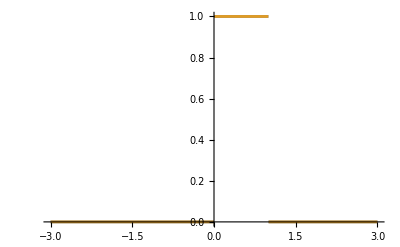

```mathematica
Plot[{HeavisideTheta[x]-HeavisideTheta[x-1],HeavisideTheta[x]HeavisideTheta[1-x]},{x,-3,3}]
```

```mathematica
f1313[x_,y_,X_]:=(((1-x)x)/(X-x)^2)(HeavisideTheta[x+y]HeavisideTheta[1-(x+y)]);
f2323[x_,y_,X_]:=(((1-y)y)/(X-y)^2)(HeavisideTheta[x+y]HeavisideTheta[1-(x+y)]);
f1323[x_,y_,X_]:=(x*y)/((X-x)(X-y))(HeavisideTheta[x+y]HeavisideTheta[1-(x+y)]);
```

```mathematica
Assuming[{X>0,X>1},Integrate[Integrate[f1313[x,y,X],{y,0,1}],{x,0,1}]]
```

1/2 (-5+6 X+4 ArcCoth[1-2 X]-16 X ArcCoth[1-2 X]+12 X^2 ArcCoth[1-2 X])

```mathematica
FullSimplify[1/2 (-5+6 X+4 ArcCoth[1-2 X]-16 X ArcCoth[1-2 X]+12 X^2 ArcCoth[1-2 X])]
```

-5/2+3 X+(2-8 X+6 X^2) ArcCoth[1-2 X]

```mathematica
f[X_]:=-5/2+3 X+(2-8 X+6 X^2) ArcCoth[1-2 X];
h1[X_]:=-5/2+3 X-(1-4 X+3 X^2) Log[X/(X-1)];
```

```mathematica
g[X_]:=1/2 (1-4 X+4 X Log[(-1+X)/X]-4 X^2 Log[(-1+X)/X]+2 X^2 Log[2-1/X] Log[(-1+X)/X]-2 X^2 PolyLog[2,(-1+X)/(-1+2 X)]+2 X^2 PolyLog[2,X/(-1+2 X)]);
```

```mathematica
h2[X_]:=1/2-2X-π^2/6 X^2+2(X-1)X*Log[X/(X-1)]+X^2 Log[X/(2X-1)]^2+2 X^2 PolyLog[2,X/(2X-1)];
```

```mathematica
Series[h1[x],{x,∞,2}]
```

1/(12 x^2)+O[1/x]^3

```mathematica
Series[h2[x],{x,∞,2}]
```

1/(24 x^2)+O[1/x]^3

```mathematica
1/6+4/12
```

```mathematica
12*512
```

6144

```mathematica
g[10]
```

55/2-261 (ⅈ π+Log[10/9])

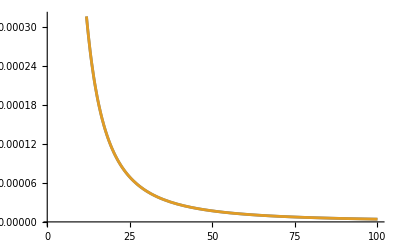

```mathematica
Plot[{g[X],h2[X]},{X,1,100}]
```

```mathematica
Assuming[{X>0,X>1},Integrate[Integrate[f1323[x,y,X],{x,0,1}],{y,0,1}]]
```

1/2 (1-4 X+4 X Log[(-1+X)/X]-4 X^2 Log[(-1+X)/X]+2 X^2 Log[2-1/X] Log[(-1+X)/X]-2 X^2 PolyLog[2,(-1+X)/(-1+2 X)]+2 X^2 PolyLog[2,X/(-1+2 X)])

```mathematica
Assuming[{X>1},FullSimplify[1/2 (1-4 X+4 X Log[(-1+X)/X]-4 X^2 Log[(-1+X)/X]+2 X^2 Log[2-1/X] Log[(-1+X)/X]-2 X^2 PolyLog[2,(-1+X)/(-1+2 X)]+2 X^2 PolyLog[2,X/(-1+2 X)])]]
```

1/2-2 X+X (2-2 X+X Log[2-1/X]) Log[(-1+X)/X]+X^2 (-PolyLog[2,(-1+X)/(-1+2 X)]+PolyLog[2,X/(-1+2 X)])

```mathematica
FullSimplify[1/2-2 X+X (2-2 X+X Log[2-1/X]) Log[(-1+X)/X]+X^2 (-PolyLog[2,(-1+X)/(-1+2 X)]+PolyLog[2,X/(-1+2 X)])]
```

1/2-2 X+X (2-2 X+X Log[2-1/X]) Log[(-1+X)/X]+X^2 (-PolyLog[2,(-1+X)/(-1+2 X)]+PolyLog[2,X/(-1+2 X)])

```mathematica
FullSimplify[(1/2-2 X+X (2-2 X+X Log[2-1/X]) Log[(-1+X)/X]+X^2 (-PolyLog[2,(-1+X)/(-1+2 X)]+PolyLog[2,X/(-1+2 X)]))/.{PolyLog[2,(-1+X)/(-1+2 X)]->-PolyLog[2,X/(-1+2 X)]-Log[1-X/(-1+2 X)]Log[X/(-1+2 X)]+π^2/6}]
```

1/2-2 X+X (2-2 X+X Log[2-1/X]) Log[(-1+X)/X]+X^2 (-π^2/6+Log[(-1+X)/(-1+2 X)] Log[X/(-1+2 X)]+2 PolyLog[2,X/(-1+2 X)])

```mathematica
FullSimplify[(2x-1+1)/(2x-1-1)]
```

x/(-1+x)

```mathematica
Assuming[{X>1},FullSimplify[1/2-2 X+X (2-2 X-X Log[X/(-1+2X)]) Log[(-1+X)/X]+X^2 (-π^2/6+Log[(-1+X)/(-1+2 X)] Log[X/(-1+2 X)]+2 PolyLog[2,X/(-1+2 X)])]]
```

1/2-1/6 X (12+π^2 X)-4 (-1+X) X ArcCoth[1-2 X]+X^2 Log[X/(-1+2 X)]^2+2 X^2 PolyLog[2,X/(-1+2 X)]

```mathematica
ArcCoth[-10]
```

-ArcCoth[10]

```mathematica
Plot[{1/2-2 X+X (2-2 X+X Log[2-1/X]) Log[(-1+X)/X]+X^2 (-PolyLog[2,(-1+X)/(-1+2 X)]+PolyLog[2,X/(-1+2 X)]),1/2-1/6 X (12+π^2 X)-4 (-1+X) X ArcCoth[1-2 X]+X^2 Log[X/(-1+2 X)]^2+2 X^2 PolyLog[2,X/(-1+2 X)]},{X,1,100}]
```

-Graphics-

```mathematica
FullSimplify[((-1+X)/(-1+2 X))+(X/(-1+2 X))]
```

1

```mathematica
FullSimplify[(PolyLog[2,z]-PolyLog[2,1-z])/.{z->X/(-1+2 X)}]
```

-PolyLog[2,(-1+X)/(-1+2 X)]+PolyLog[2,X/(-1+2 X)]

```mathematica
g[X_]:=1/2-2 X+X (2-2 X+X Log[2-1/X]) Log[(-1+X)/X]+X^2 (-PolyLog[2,(-1+X)/(-1+2 X)]+PolyLog[2,X/(-1+2 X)]);
```

```mathematica
Series[f[X],{X,∞,4}]
```

1/(12 X^2)+1/(15 X^3)+1/(20 X^4)+O[1/X]^5

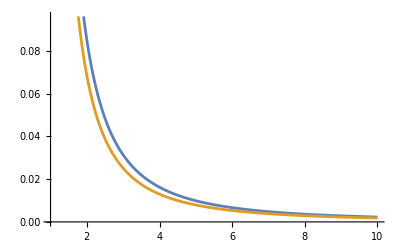

```mathematica
Plot[{2f[X]+g[X],2f[X]},{X,1,10}]
```

```mathematica
Γijjk=1/(2π)^3*mi/32(2f[X]+g[X]);
Γijkl=1/(2π)^3*mi/32 f[X];
```

```mathematica
Series[Γijjk,{X,∞,2}]
```

(5 mi)/(6144 π^3 X^2)+O[1/X]^3

```mathematica
Series[Γijkl,{X,∞,2}]
```

mi/(3072 π^3 X^2)+O[1/X]^3

```mathematica
32*8*π^3
```

256 π^3